## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/chaos_meets_channels/ja_files

```mathematica
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
IPR[ψ_]:=Total[ψ^4]
```

## Cálculos

Construir el Hamiltoniano del XXZ

### ϵ_d=0

```mathematica
{Jxy,Jz,ω,ϵd,L,d}={1.,1.,0.,0.0,7,2};
```

```mathematica
iprsVsJxy=Table[
H=LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵd,L,d];
{eigvals,eigvecs}=Chop[Eigensystem[H]];
iprs=IPR/@eigvecs;
{Jxy,Mean[iprs]}
,{Jxy,0,5,0.25}]
```

{{0.,1.},{0.25,0.236939},{0.5,0.172571},{0.75,0.129527},{1.,0.103935},{1.25,0.109368},{1.5,0.106338},{1.75,0.106892},{2.,0.103249},{2.25,0.103627},{2.5,0.102818},{2.75,0.101672},{3.,0.0990194},{3.25,0.0989893},{3.5,0.0979691},{3.75,0.0988383},{4.,0.0972688},{4.25,0.0993697},{4.5,0.0994857},{4.75,0.0976732},{5.,0.100051}}

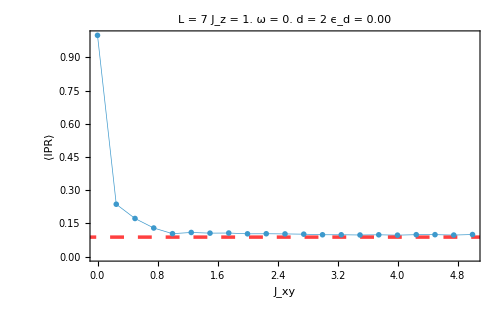

```mathematica
imgSize=500;
ListPlot[iprsVsJxy,
PlotRange->Full,
Joined->True,
PlotMarkers->{Automatic,imgSize/40},
PlotStyle->Directive[Thickness[0.001]],
Frame->True,
FrameStyle->Directive[Black,FontSize->N[Sqrt[imgSize]]],
FrameLabel->{TraditionalForm[HoldForm[Subscript[J, xy]]], "⟨IPR⟩"},
PlotLabel->Style["L = "<>ToString[NumberForm[L,{Infinity,0}]]<>" J_z = "<>ToString[NumberForm[Jz,{Infinity,0}]]<>" ω = "<>ToString[NumberForm[ω,{Infinity,0}]]<>" d = "<>ToString[NumberForm[d,{Infinity,0}]]<>" ϵ_d = "<>ToString[NumberForm[ϵd,{Infinity,2}]]
,Black,FontSize->N[Sqrt[imgSize]]],
ImageSize->imgSize,
Epilog->{Red,Thickness[0.005],Dashing[0.02],Opacity[0.75],InfiniteLine[{{0,#},{5,#}}]&[Sqrt[(1/2.^L)]]}
]
```

### ϵ_d=0.01

```mathematica
{Jxy,Jz,ω,ϵd,L,d}={1.,1.,0.,0.01,7,2};
```

```mathematica
iprsVsJxy=Table[
H=LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵd,L,d];
{eigvals,eigvecs}=Chop[Eigensystem[H]];
iprs=IPR/@eigvecs;
{Jxy,Mean[iprs]}
,{Jxy,0,5,0.25}]
```

{{0.,1.},{0.25,0.337082},{0.5,0.221016},{0.75,0.146332},{1.,0.120932},{1.25,0.116129},{1.5,0.113566},{1.75,0.11165},{2.,0.110114},{2.25,0.109439},{2.5,0.108433},{2.75,0.107653},{3.,0.106986},{3.25,0.106586},{3.5,0.106207},{3.75,0.105892},{4.,0.105621},{4.25,0.105386},{4.5,0.105179},{4.75,0.104997},{5.,0.104836}}

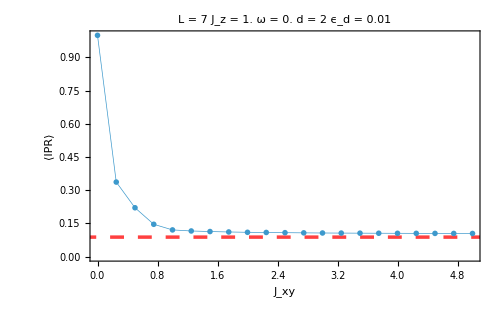

```mathematica
imgSize=500;
ListPlot[iprsVsJxy,
PlotRange->Full,
Joined->True,
PlotMarkers->{Automatic,imgSize/40},
PlotStyle->Directive[Thickness[0.001]],
Frame->True,
FrameStyle->Directive[Black,FontSize->N[Sqrt[imgSize]]],
FrameLabel->{TraditionalForm[HoldForm[Subscript[J, xy]]], "⟨IPR⟩"},
PlotLabel->Style["L = "<>ToString[NumberForm[L,{Infinity,0}]]<>" J_z = "<>ToString[NumberForm[Jz,{Infinity,0}]]<>" ω = "<>ToString[NumberForm[ω,{Infinity,0}]]<>" d = "<>ToString[NumberForm[d,{Infinity,0}]]<>" ϵ_d = "<>ToString[NumberForm[ϵd,{Infinity,2}]]
,Black,FontSize->N[Sqrt[imgSize]]],
ImageSize->imgSize,
Epilog->{Red,Thickness[0.005],Dashing[0.02],Opacity[0.75],InfiniteLine[{{0,#},{5,#}}]&[Sqrt[(1/2.^L)]]}
]
```

### ϵ_d=5

```mathematica
{Jxy,Jz,ω,ϵd,L,d}={1.,1.,0.,5,7,2};
```

```mathematica
iprsVsJxy=Table[
H=LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵd,L,d];
{eigvals,eigvecs}=Chop[Eigensystem[H]];
iprs=IPR/@eigvecs;
{Jxy,Mean[iprs]}
,{Jxy,0,5,0.25}]
```

{{0.,1.},{0.25,0.561213},{0.5,0.454807},{0.75,0.340554},{1.,0.289428},{1.25,0.251509},{1.5,0.226488},{1.75,0.212919},{2.,0.203187},{2.25,0.196602},{2.5,0.191373},{2.75,0.185011},{3.,0.17751},{3.25,0.171994},{3.5,0.169795},{3.75,0.165035},{4.,0.161664},{4.25,0.157745},{4.5,0.15408},{4.75,0.150111},{5.,0.147661}}

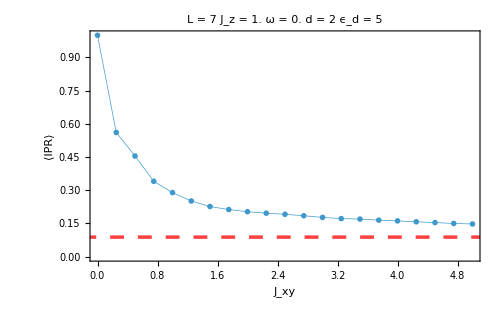

```mathematica
imgSize=500;
ListPlot[iprsVsJxy,
PlotRange->Full,
Joined->True,
PlotMarkers->{Automatic,imgSize/40},
PlotStyle->Directive[Thickness[0.001]],
Frame->True,
FrameStyle->Directive[Black,FontSize->N[Sqrt[imgSize]]],
FrameLabel->{TraditionalForm[HoldForm[Subscript[J, xy]]], "⟨IPR⟩"},
PlotLabel->Style["L = "<>ToString[NumberForm[L,{Infinity,0}]]<>" J_z = "<>ToString[NumberForm[Jz,{Infinity,0}]]<>" ω = "<>ToString[NumberForm[ω,{Infinity,0}]]<>" d = "<>ToString[NumberForm[d,{Infinity,0}]]<>" ϵ_d = "<>ToString[NumberForm[ϵd,{Infinity,2}]]
,Black,FontSize->N[Sqrt[imgSize]]],
ImageSize->imgSize,
Epilog->{Red,Thickness[0.005],Dashing[0.02],Opacity[0.75],InfiniteLine[{{0,#},{5,#}}]&[Sqrt[(1/2.^L)]]}
]
```

### Mapa de IPR promedio de todos los eigenvectores

```mathematica
{Jz,ω,L,d}={1.,0.,7,3};
```

```mathematica
mapIPRs={};
```

```mathematica
Do[
H=LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵd,L,d];
{eigvals,eigvecs}=Chop[Eigensystem[H]];
iprs=IPR/@eigvecs;
AppendTo[mapIPRs,{ϵd,Jxy,Mean[iprs]}];
,{ϵd,Subdivide[0.,5.,109]}
,{Jxy,Subdivide[0.,5.,109]}]
```

```mathematica
fontSize=20;
```

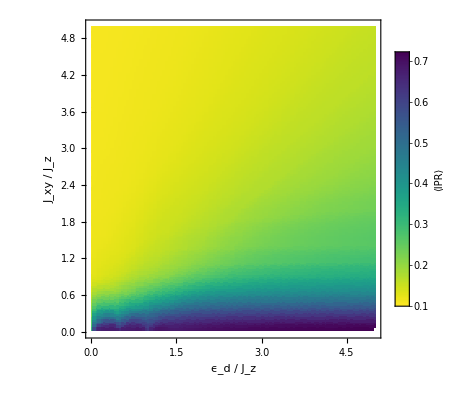

```mathematica
ListDensityPlot[mapIPRs,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[mapIPRs[[All,3]]],Max[Select[mapIPRs[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨IPR⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ϵ_d / J_z","J_xy / J_z"},
AspectRatio->1
]
```

Debería de tomar el promedio del IPR sólo de los eigenvectores de un subespacio simétrico?

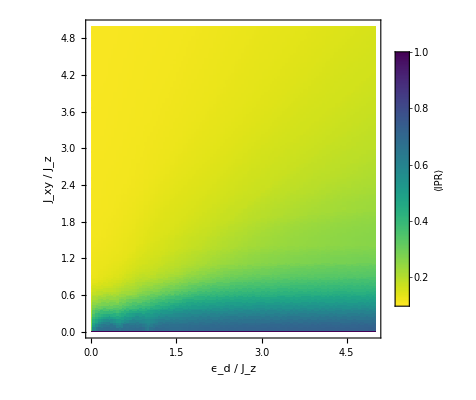

```mathematica
ListDensityPlot[mapIPRs,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[mapIPRs[[All,3]]],1},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨IPR⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ϵ_d / J_z","J_xy / J_z"},
AspectRatio->1
]
```